Total time for generating DensityPlot and Plot3D: 17.2399 minutes

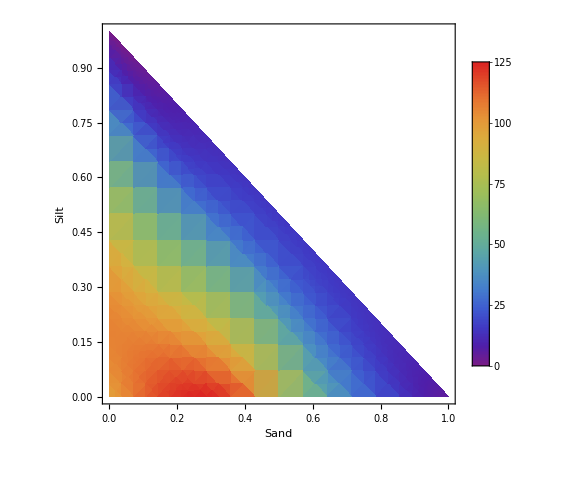

-Graphics3D-

```mathematica
(*Written by Frederic Ouimet (August 2024)*)

(*Define the necessary functions*)
hatM[xx_,b_,s_,y_]:=Module[{n,d,u,v,kernelVec,designMat,W},
n=Length[xx];
d=Length[xx[[1]]];

(*Calculate kernel vector*)
u=s/b+ConstantArray[1,d];
v=(1-Total[s])/b+1;
kernelVec=Table[PDF[DirichletDistribution[Join[u,{v}]],xx[[i]]],{i,1,n}];

(*Local Linear Estimation*)
designMat=Table[Join[{1},xx[[i]]-s],{i,1,n}];
W=DiagonalMatrix[kernelVec];
Return[First[LinearSolve[Transpose[designMat].W.designMat,Transpose[designMat].W.y]]];
];

(*Data 5 from Aitchison (p.359)*)
vectors={{77.5,19.5,3.0,10.4},{71.9,24.9,3.2,11.7},{50.7,36.1,13.2,12.8},{52.2,40.9,6.6,13.0},{70.0,26.5,3.5,15.7},{66.5,32.2,1.3,16.3},{43.1,55.3,1.6,18.0},{53.4,36.8,9.8,18.7},{15.5,54.4,30.1,20.7},{31.7,41.5,26.8,22.1},{65.7,27.8,6.5,22.4},{70.4,29.0,0.6,24.4},{17.4,53.6,29.0,25.8},{10.6,69.8,19.6,32.5},{38.2,43.1,18.7,33.6},{10.8,52.7,36.5,36.8},{18.4,50.7,30.9,37.8},{4.6,47.4,48.0,36.9},{15.6,50.4,34.0,42.2},{31.9,45.1,23.0,47.0},{9.5,53.5,37.0,47.1},{17.1,48.0,34.9,48.4},{10.5,55.4,34.1,49.4},{4.8,54.7,41.0,49.5},{2.6,45.2,52.2,59.2},{11.4,52.7,35.9,60.1},{6.7,46.9,46.4,61.7},{6.9,49.7,43.4,62.4},{4.0,44.9,51.1,69.3},{7.4,51.6,40.9,73.6},{4.8,49.5,45.7,74.4},{4.5,48.5,47.0,78.5},{6.6,52.1,41.3,82.9},{6.7,47.3,45.9,87.7},{7.4,45.6,46.9,88.1},{6.0,48.9,45.1,90.4},{6.3,53.8,39.9,90.6},{2.5,48.0,49.5,97.7},{2.0,47.8,50.2,103.7}};

(*Extract xx and y from the given vectors*)
xx=(vectors[[All,1;;2]])/100;
y=vectors[[All,4]];

(*Optimal b (b_opt_LOOCV from R)*)
b=0.219521406430846;

hatMFunction[s1_,s2_]:=hatM[xx,b,{s1,s2},y];

(*Measure time for DensityPlot and Plot3D*)
time=AbsoluteTiming[
(*Create density plot*)densityPlot=DensityPlot[Evaluate[hatMFunction[s1,s2]],{s1,0,1},{s2,0,1},RegionFunction->Function[{s1,s2},s1+s2<=1],PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->300,LabelStyle->Directive[FontSize->18]],Right],ColorFunction->"Rainbow",Frame->True,FrameLabel->{Style["Sand",FontSize->22],Style["Silt",FontSize->22]},TicksStyle->Directive[FontSize->18],LabelStyle->Directive[FontSize->18]];

(*Create 3D plot*)plot3D=Plot3D[Evaluate[hatMFunction[s1,s2]],{s1,0,1},{s2,0,1},RegionFunction->Function[{s1,s2,z},s1+s2<=1],ColorFunction->"Rainbow",AxesLabel->{Style["Sand",FontSize->22],Style["Silt",FontSize->22],Style["Water depth",FontSize->22]},TicksStyle->Directive[FontSize->18]
];][[1]]; (*Extract the time value*)


(*Convert time to minutes*)
timeInMinutes=time/60;

(*Display time difference*)
Print["Total time for generating DensityPlot and Plot3D: ",timeInMinutes," minutes"]

(*Display plots*)
Show[densityPlot]
Show[plot3D]
```